Import the data:

```mathematica
rxpkp = Import["~/Desktop/underfive.csv"]⟦2;;⟧;
```

```mathematica
rxpkp⟦Range[1,10]⟧
```

{{0,177.1},{1,180.679},{2,181.387},{3,162.501},{4,138.025},{5,107.407},{6,84.2726},{7,76.7897},{8,80.8254},{9,109.721}}

Plot the data:

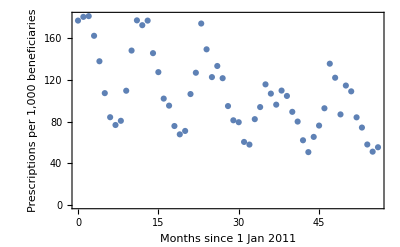

```mathematica
ListPlot[rxpkp,Frame->{True,True,False,False}, FrameLabel->{"Months since 1 Jan 2011","Prescriptions per 1,000 beneficiaries"}, BaseStyle->FontSize->12]
```

Fit the sinusoid:
β0: intercept of the upper trend line (peak monthly prescribing rate per 1,000 beneficiaries)
β1: slope of the upper trend line (peak monthly prescribing rate per 1,000 beneficiaries)
γ0: intercept of the lower trend line (trough monthly prescribing rate per 1,000 beneficiaries)
γ1: slope of the lower trend line (trough monthly prescribing rate per 1,000 beneficiaries)
δ: phase shift of the sinusoid

```mathematica
upper[x_] := β0 + β1 x  ; (*The upper trend line*)
lower[x_] := γ0 + γ1 x  ; (*The lower trend line*)
```

```mathematica
fit = NonlinearModelFit[rxpkp, {
1/2 (upper[x] + lower[x]) + 1/2 (upper[x] - lower[x])( Cos[(2 π)/12 (x - δ)] )
},{β0, β1, γ0,γ1, δ},x];
```

```mathematica
fit
```

FittedModel[1/2 (274.494-2.21045 x)+1/2 (108.275-1.16668 x) Cos[1/6 π (-0.658059+x)]]

```mathematica
Normal[fit]
```

1/2 (274.494-2.21045 x)+1/2 (108.275-1.16668 x) Cos[1/6 π (-0.658059+x)]

```mathematica
fit["BestFitParameters"]
```

{β0→191.384,β1→-1.68856,γ0→83.1096,γ1→-0.521889,δ→0.658059}

```mathematica
fit["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
β0 | 191.384 | 5.61896 | {180.109,202.659}
β1 | -1.68856 | 0.181924 | {-2.05362,-1.32351}
γ0 | 83.1096 | 6.06145 | {70.9464,95.2727}
γ1 | -0.521889 | 0.176705 | {-0.876474,-0.167303}
δ | 0.658059 | 0.123528 | {0.410181,0.905937}

Plot the output:

```mathematica
fitplot = Plot[fit[x], {x,rxpkp⟦1,1⟧,rxpkp⟦-1,1⟧}, PlotRange->All, PlotStyle->Black, PlotLegends->{"Sinusoid fit"}];
```

```mathematica
upperplot = Plot[upper[x]/.fit["BestFitParameters"], {x,rxpkp⟦1,1⟧,rxpkp⟦-1,1⟧}, PlotStyle->Blue, PlotLegends->{"Envelope"}];
lowerplot = Plot[lower[x]/.fit["BestFitParameters"], {x,rxpkp⟦1,1⟧,rxpkp⟦-1,1⟧}, PlotStyle->Blue];
```

```mathematica
dataplot = ListLinePlot[rxpkp,PlotMarkers->Automatic, PlotStyle->{Gray}, PlotRange->All, PlotLegends->{"Data"}];
```

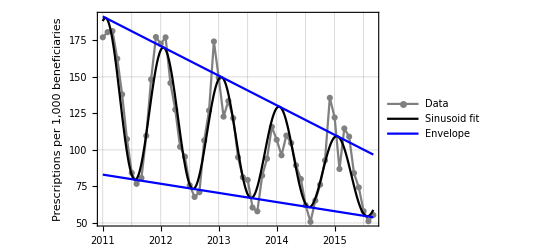

```mathematica
figunder5sinusoid = Show[dataplot, fitplot, upperplot, lowerplot, PlotRange->{0, Automatic}, Frame->{True,True,False,False}, FrameLabel->{None,"Prescriptions per 1,000\nbeneficiaries"}, BaseStyle->FontSize->14, ImageSize->400,
FrameTicks->{{{0, "2011"},{12, "2012"},{24, "2013"},{36, "2014"},{48, "2015"}},Automatic}, GridLines->{Table[i,{i,0,54,6}],{50,100,150,200}}]
```